```mathematica
(*First make sure you clear the kernel*)
Quit[];
```

0.022012

0.021688

0.512492

0.512492

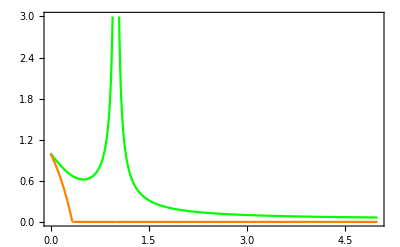

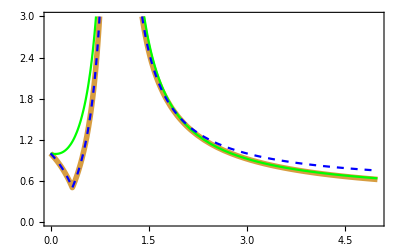

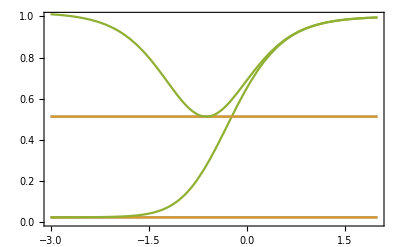

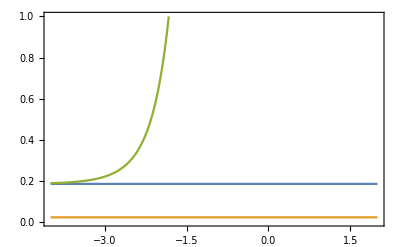

```mathematica
(*Run this code to generate the plots in Figure 1*)
chiSpecial1[psi_, zetasq_] := -(1/2) *(((psi*zetasq - zetasq -1)^2 + 4 * zetasq * psi)^(1/2) + (psi*zetasq -
zetasq -1)) / zetasq;
d0Special1[zetasq_,psi1_,psi2_]:=Module[{chival},chival=chiSpecial1[Min[psi1,psi2],zetasq];
chival^5*zetasq^3 - 3*chival^4*zetasq^2-(psi1*psi2-psi2-psi1+1)*chival^3*zetasq^3 + 2*chival^3*zetasq^2 + 3*chival^3*zetasq -(psi1+psi2-3*psi1*psi2+1)*chival^2*zetasq^2 - 2*chival^2*zetasq - chival^2 - 3*psi1*psi2*chival*zetasq + psi1*psi2];
d0Special1mod[zetasq_,psi1_,psi2_, chi_]:=Module[{chival},chival= chi;
chival^5*zetasq^3 - 3*chival^4*zetasq^2-(psi1*psi2-psi2-psi1+1)*chival^3*zetasq^3 + 2*chival^3*zetasq^2 + 3*chival^3*zetasq -(psi1+psi2-3*psi1*psi2+1)*chival^2*zetasq^2 - 2*chival^2*zetasq - chival^2 - 3*psi1*psi2*chival*zetasq + psi1*psi2];
d1Special1[zetasq_,psi1_,psi2_]:=Module[{chival},chival=chiSpecial1[Min[psi1,psi2],zetasq];chival^6*zetasq^3 - 2*chival^5*zetasq^2-(psi1*psi2-psi1-psi2+1)*chival^4*zetasq^3 + chival^4*zetasq^2 + chival^4*zetasq -2*(1-(psi1 * psi2))*chival^3*zetasq^2 -(psi1 + psi2 + psi1*psi2 + 1)*chival^2*zetasq  - chival^2];
d1Special1mod[zetasq_,psi1_,psi2_, chi_]:=Module[{chival},chival=chi;chival^6*zetasq^3 - 2*chival^5*zetasq^2-(psi1*psi2-psi1-psi2+1)*chival^4*zetasq^3 + chival^4*zetasq^2 + chival^4*zetasq -2*(1-(psi1 * psi2))*chival^3*zetasq^2 -(psi1 + psi2 + psi1*psi2 + 1)*chival^2*zetasq  - chival^2];
d2Special1 [zetasq_,psi1_,psi2_]:=Module[{chival},chival=chiSpecial1[Min[psi1,psi2],zetasq];
-(psi1-1)*chival^3 * zetasq^2 - chival^3 * zetasq + (psi1+1)*chival^2*zetasq + chival^2];
d2Special1mod [zetasq_,psi1_,psi2_, chi_]:=Module[{chival},chival=chi;
-(psi1-1)*chival^3 * zetasq^2 - chival^3 * zetasq + (psi1+1)*chival^2*zetasq + chival^2];
SSpecial1[F1_, Fs_, tau_,psi1_,psi2_,zetasq_]:=
Module[{chival},chival=chiSpecial1[Min[psi1,psi2],zetasq];
F1^2 *(zetasq)*(d1Special1[zetasq,psi1,psi2]/((chival *(zetasq) -1 )*d0Special1[zetasq,psi1,psi2]))+ (tau^2+Fs^2)*(zetasq)* (d2Special1[zetasq,psi1,psi2]/d0Special1[zetasq,psi1,psi2])];
Sm[F1_, Fs_, tau_,psi1_,psi2_,mu0_,mu1_,mu2_]:=
Module[{chival,zetasq},zetasq=(mu1^2/(mu2-mu0^2-mu1^2));chival=chiSpecial1[Min[psi1,psi2],zetasq];
F1^2 *(zetasq)*(d1Special1[zetasq,psi1,psi2]/((chival *(zetasq) -1 )*d0Special1[zetasq,psi1,psi2]))+ (tau^2+Fs^2)*(zetasq)* (d2Special1[zetasq,psi1,psi2]/d0Special1[zetasq,psi1,psi2])];
eps0[zetasq_, psi1_, psi2_] :=Module[{chival}, chival = chiSpecial1[Min[psi1, psi2], zetasq];
-chival^5*zetasq^3+3*chival^4*zetasq^2+(psi1*psi2-psi2-psi1+1)*chival^3*zetasq^3-2*chival^3*zetasq^2-3*chival^3*zetasq+(psi1+psi2-3*psi1*psi2+1)*chival^2*zetasq^2+2*chival^2*zetasq+chival^2+3*psi1*psi2*chival*zetasq-psi1*psi2];
eps1[zetasq_, psi1_, psi2_] := Module[{chival}, chival = chiSpecial1[Min[psi1, psi2], zetasq];
psi2*chival^3*zetasq^2-psi2*(chival^2)*zetasq+psi1*psi2*chival*zetasq-psi1*psi2];
eps2[zetasq_, psi1_, psi2_] := Module[{chival}, chival = chiSpecial1[Min[psi1, psi2], zetasq];chival^5*zetasq^3-3*chival^4*zetasq^2+(psi1-1)*chival^3*zetasq^3+2*chival^3*zetasq^2+3*chival^3*zetasq+(-psi1-1)*(chival^2)*(zetasq^2)-2*(chival^2)*zetasq-(chival^2)];
B[zetasq_, psi1_, psi2_] := eps1[zetasq, psi1, psi2] /eps0[zetasq, psi1, psi2];
V[zetasq_, psi1_, psi2_] := eps2[zetasq, psi1, psi2] /eps0[zetasq, psi1, psi2];
R[F1_,Fs_,tau_,psi1_,psi2_,zetasq_] := Re[F1^2*B[zetasq,psi1,psi2]+(Fs^2+tau^2)*V[zetasq,psi1,psi2]+Fs^2];
Rm[F1_,Fs_,tau_,psi1_,psi2_,mu0_,mu1_,mu2_] := Re[F1^2*B[(mu1^2/(mu2-mu0^2-mu1^2)),psi1,psi2]+(Fs^2+tau^2)*V[(mu1^2/(mu2-mu0^2-mu1^2)),psi1,psi2]+Fs^2];
ObjectiveR1[F1_,Fs_,tau_,psi1_,psi2_,mu0_,mu1_,mu2_,α_] := (1-α)*Rm[F1,Fs,tau,psi1,psi2,mu0,mu1,mu2]+α*Sm[F1,Fs,tau,psi1,psi2,mu0,mu1,mu2];
OptimalObjectiveSpecialCase1AlphaZero[F1_,Fs_,psi1_,psi2_,tau_]:=Which[psi1>psi2,(F1^2 psi1 (Max[1-psi2,0])^2+(psi1-psi2 + Abs[1-psi2]*Max[psi2,1]) *Min[psi2,1]*(Fs^2+tau^2))/((psi1-psi2) Abs[-1+psi2])+Fs^2,psi1<psi2,
(Fs^2 psi2+F1^2 Max[1-psi1,0] psi2+psi1 tau^2)/(psi2-psi1)];
PolyPsi1GreaterPsi2[chi_,psi2_,F1_,Fs_,psi1_,tau_,α_]:=-2 chi^5 F1^2 α+4 chi^3 psi2 ((Fs^2+tau^2) α-F1^2 (psi2-2 (1+psi1) α+6 psi2 α))+psi2^2 (Fs^2 (2 psi1-2 psi2+(-1+psi2)^2 α)+tau^2 (2 psi1-2 psi2+(-1+psi2)^2 α)-F1^2 (-1+psi2)^2 (psi2+(-1-2 psi1+3 psi2) α))+chi^4 ((Fs^2+tau^2) α+F1^2 (α+2 psi1 α-psi2 (1+11 α)))+2 chi (psi2 (Fs^2+tau^2) (psi1+psi2 (-1+2 (-1+psi2) α))-F1^2 (-1+psi2) psi2 (psi1-4 psi1 psi2 α+psi2 (-1+2 psi2-3 α+7 psi2 α)))+2 chi^2 (psi2 (-1+3 psi2) (Fs^2+tau^2) α-F1^2 psi2 (psi1+α+psi1 (2-6 psi2) α+psi2 (-2+3 psi2-10 α+13 psi2 α)));
objectiveR1Psi1GreaterPsi2[chi_,psi2_,F1_,Fs_,psi1_,tau_,α_]:=(-chi^4 F1^2 α-psi2 ((1+psi1-2 psi2) psi2 tau^2+Fs^2 (psi1-psi2^2+(psi1-psi2) (-1+psi2) α)+F1^2 (-1+psi2) (psi1 (-1+psi2)+(-psi1+psi2) (-1+2 psi2) α))+chi^2 (Fs^2 (psi2-psi1 α+3 psi2 α)+F1^2 (-psi2 (-1+psi1+2 psi2)+(4-9 psi2) psi2 α+psi1 (-1+6 psi2) α)+tau^2 (-psi1+2 psi2 (1+α)))-chi psi2 (Fs^2 (-2 psi2+α+2 psi1 α-3 psi2 α)+F1^2 ((-1+psi2) (2 psi1+psi2)+(1+4 psi1-6 (1+psi1) psi2+7 psi2^2) α)+tau^2 (2 psi1+α-psi2 (4+α)))+chi^3 ((Fs^2+tau^2) α+F1^2 (α+2 psi1 α-psi2 (1+5 α))))/((psi1-psi2) (-psi2+(chi+psi2)^2));
F1=1;
Fs=0.00;
tau=0;
mu0=0.398942;
mu1=0.5;
mu2=0.5;
alpha = 0;
psi2=3;
g0=Plot[{ObjectiveR1[F1,Fs,tau,x*psi2,psi2,mu0,mu1,mu2,alpha],OptimalObjectiveSpecialCase1AlphaZero[F1,Fs,x*psi2,psi2,tau]},{x,0,5},PlotRange->{0,3},Frame->True,PlotStyle->{Green,Orange}];
tau=1;
x1[psi1_]:=Solve[PolyPsi1GreaterPsi2[chi,psi2,F1,Fs,psi1,tau,alpha]==0,chi];
Lb=-psi2;
Ub=Min[0,1-psi2];
realQ=NumberQ[#]&&!MatchQ[#,_Complex]&;
x11[psi1_]:=If[Length[Select[x1[psi1][[;;,1,2]],(realQ[#]&&(#≥Lb)&&(#≤Ub))&]]>0,Select[x1[psi1][[;;,1,2]],(realQ[#]&&(#≥Lb)&&(#≤Ub))&][[1]],Ub];
g1=Plot[Which[x*psi2>psi2,objectiveR1Psi1GreaterPsi2[x11[x*psi2],psi2,F1,Fs,x*psi2,tau,alpha],x*psi2≤psi2,OptimalObjectiveSpecialCase1AlphaZero[F1,Fs,x*psi2,psi2,tau]],{x,0,5},Frame->True,PlotStyle->{RGBColor[215/255,157/255,65/255],Thickness[0.01]},PlotRange->{0,3},PlotStyle->Orange];
g2=Plot[{ObjectiveR1[F1,Fs,tau,x*psi2,psi2,mu0,mu1,mu2,alpha],OptimalObjectiveSpecialCase1AlphaZero[F1,Fs,x*psi2,psi2,tau]},{x,0,5},PlotRange->{0,3},Frame->True,PlotStyle->{Green,{Blue,Dashed}}];
w[psi2_, zetasq_, lambdabar_] := -(((psi2*zetasq - zetasq - lambdabar*psi2 -1)^2 + 4*psi2*zetasq*(lambdabar*psi2 + 1))^(1/2) + (psi2*zetasq - zetasq - lambdabar*psi2 - 1))/(2*(lambdabar*psi2 + 1));
B[zetasq_, psi2_, lambdabar_] := Module [{wval}, wval = w[psi2, zetasq, lambdabar]; 
(psi2*wval - psi2)/((psi2-1)*wval^3 + (1-3*psi2)*wval^2 + 3*psi2*wval - psi2)];
V[zetasq_, psi2_, lambdabar_] := Module[{wval}, wval = w[psi2, zetasq, lambdabar];
(wval^3 - wval^2)/((psi2-1)*wval^3 + (1-3*psi2)*wval^2 + 3*psi2*wval - psi2)];
Rsimpler[F1_,Fs_,tau_, psi2_, lambda_, zetasq_,mussq_] := F1^2*B[(zetasq),psi2,(lambda/(mussq))]+(Fs^2+tau^2)*V[(zetasq),psi2,(lambda/(mussq))]+Fs^2;
F1=1;
Fs=0;
tau=√(1/5);
psi2=10;
mu0=0.398942;
mu1=0.5;
mu2=0.5;
mussq=mu2-mu1^2-mu0^2;
zetasq=mu1^2/mussq;
bestval=NMinimize[{Rsimpler[F1,Fs,tau, psi2, lambdatmp, zetasq,mussq],lambdatmp≥0},lambdatmp][[1]]
bestvalAF[lambda_]:=NMinimize[{Rsimpler[F1,Fs,tau, psi2, lambda, zetasqtmp,mussqtmp],zetasqtmp≥0&&mussqtmp≥0},{zetasqtmp,mussqtmp}][[1]];
bestvalAF[1](*Checking the value for a specific lambda. The function is constant so any lambda will do*)
g3=Plot[{bestval,bestvalAF[10^x],Rsimpler[F1,Fs,tau, psi2, 10^x, zetasq,mussq] },{x,-3,2},PlotRange->{0,1},Frame->True];
tau=√10;
bestval=NMinimize[{Rsimpler[F1,Fs,tau, psi2, lambda, zetasq,mussq],lambda≥0},lambda][[1]]
bestvalAF[lambda_]:=NMinimize[{Rsimpler[F1,Fs,tau, psi2, lambda, zetasqtmp,mussqtmp],zetasqtmp≥0&&mussqtmp≥0},{zetasqtmp,mussqtmp}][[1]];
bestvalAF[1] (*Checking the value for a specific lambda. The function is constant so any lambda will do*)
g4=Plot[{bestval,bestvalAF[10^x],Rsimpler[F1,Fs,tau, psi2, 10^x, zetasq,mussq]} ,{x,-3,2},PlotRange->Full,Frame->True];
tau=√(1/5);
F1=10;
bestval=NMinimize[{Rsimpler[F1,Fs,tau, psi2, lambdatmp, zetasq,mussq],lambdatmp≥0},lambdatmp][[1]];
bestvalAF[lambda_]:=NMinimize[{Rsimpler[F1,Fs,tau, psi2, lambda, zetasqtmp,mussqtmp],zetasqtmp≥0&&mussqtmp≥0},{zetasqtmp,mussqtmp}][[1]];
g5=Plot[{bestval,bestvalAF[10^x],Rsimpler[F1,Fs,tau, psi2, 10^x, zetasq,mussq]} ,{x,-4,2},PlotRange->{0,1},Frame->True];
Show[g0]
Show[g1,g2]
Show[g3,g4]
Show[g5]
```